```mathematica
normalize[li_]:=Module[{},(li-Min[li])/(Max[li]-Min[li])];
```

## Shift the curve on top of each other

```mathematica
sh=+4400;
```

```mathematica
sh=0;
```

```mathematica
vari=49600+sh; (* larger values shift the blue curve left *)
```

```mathematica
cmd1:="cat C:\\Data\\somenottoobad_3.dump | ./C:\\Users\\vbush\\Documents\\git\\molecules\\twophoton\\tools\\delay -p1 -d"<>ToString[vari]<>" > /tmp/shifted.dump";
```

```mathematica
cmd2="cat /tmp/shifted.dump | ./histo -p1 -m160 > /tmp/out1.csv";
```

```mathematica
cmd3="cat /tmp/shifted.dump | ./histo -p128 -m160 > /tmp/out2.csv";
```

```mathematica
Run[cmd1];
```

```mathematica
255
```

255

```mathematica
Run[cmd2];Run[cmd3];
```

```mathematica
f1="/tmp/out1.csv";f2="/tmp/out2.csv";
```

```mathematica
data1=Drop[Import[f1,"Table"],7];data2=Drop[Import[f2,"Table"],7];
```

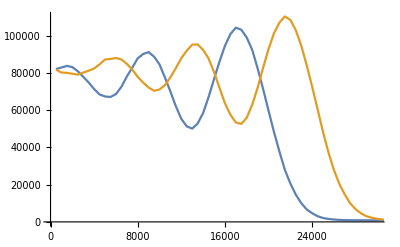

```mathematica
plot1=ListPlot[{data1⟦All,{1,2}⟧,data2⟦All,{1,2}⟧},Joined -> True,PlotRange-> {{0,30000},All}]
```

```mathematica
(* corrout=Table[{vari,
Run[cmd1];Run[cmd2];Run[cmd3];
data1=Drop[Import[f1,"Table"],7];data2=Drop[Import[f2,"Table"],7];
Total[normalize[data1⟦All,2⟧] normalize[data2⟦All,2⟧]]}
,{vari,49000,51000,20}]; *)
```

```mathematica
(* ListPlot[corrout] *)
```

## Run autocorrelation

```mathematica
cmd4="cat /tmp/shifted.dump | ./delay -p128 -d50000  | ./autocorr -t250 -m 400 > /tmp/out3.csv";
```

```mathematica
Run[cmd4];
```

```mathematica
f3="/tmp/out3.csv";
```

```mathematica
dataac=Drop[Import[f3,"Table"],7];
```

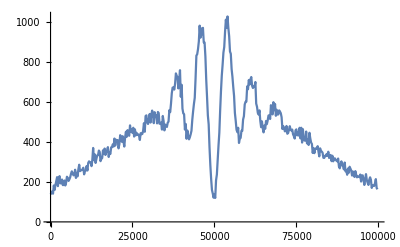

```mathematica
ListPlot[{dataac⟦All,{1,2}⟧},Joined -> True]
```

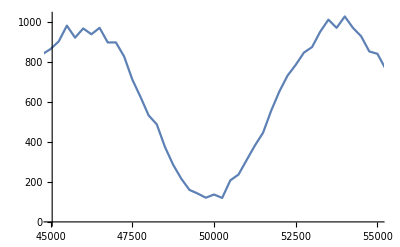

```mathematica
ListPlot[{dataac⟦All,{1,2}⟧},Joined -> True,PlotRange-> {{45000,55000},All}]
```

## Select

```mathematica
pos=22000-sh;width=700;
```

```mathematica
cmd5="cat /tmp/shifted.dump | ./select -w -t 16 -p 129 -s "<>ToString[Round[pos-width/2]]<>":"<>ToString[Round[pos+width/2]]<>" | ./histo -p1 -m160 > /tmp/out4.csv";
```

```mathematica
Run[cmd5];
```

```mathematica
f4="/tmp/out4.csv";
```

```mathematica
data4=Drop[Import[f4,"Table"],7];
```

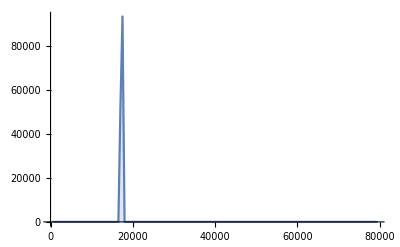

```mathematica
plot2=ListPlot[{data4⟦All,{1,2}⟧},Joined -> True,PlotRange-> All,Filling-> 0]
```

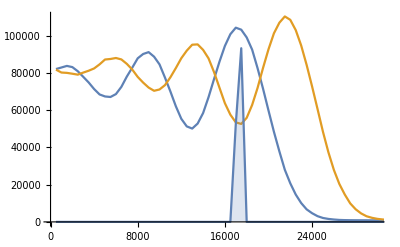

```mathematica
Show[{plot1,plot2}]
```

## Autocorr, selected

```mathematica
cmd6="cat /tmp/shifted.dump | ./select -w -t 16 -p 129 -s "<>ToString[Round[pos-width/2]]<>":"<>ToString[Round[pos+width/2]]<>" | ./delay -p128 -d4000000 | ./autocorr -t250 -m 32000 -f0.01 > /tmp/out5.csv";
```

```mathematica
Run[cmd6];
```

```mathematica
f5="/tmp/out5.csv";
```

```mathematica
data5=Drop[Import[f5,"Table"],7];
```

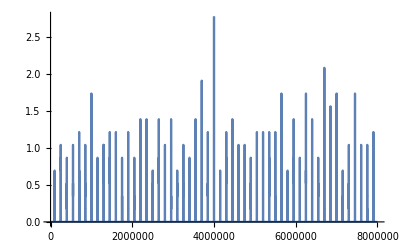

```mathematica
plot3=ListPlot[{data5⟦All,{1,3}⟧},Joined -> True,PlotRange-> All]
```

```mathematica
plot3=ListPlot[{data5⟦All,{1,2}⟧},Joined -> True,PlotRange-> {{3.99 10^6,4.01 10^6},All},GridLines-> Automatic]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

-Graphics-